# Isotropic Schwarzschild center of mass

```mathematica
M=1;
x[r_, t_, p_]:=r Sin[t] Cos[p];
y[r_, t_, p_]:=r Sin[t] Sin[p];
z[r_, t_, p_]:=r Cos[t];
normal[r_,t_,p_]:= 1/r({{x[r,t,p]}, {y[r,t,p]}, {z[r,t,p]}});
```

```mathematica
zShift = 2;
shiftedR[r_, t_, p_] := √(x[r,t,p]^2+y[r,t,p]^2+(z[r,t,p]-zShift)^2);
shiftedRGradient[r_,t_,p_]:= ({{x[r,t,p]/shiftedR[r,t,p]}, {y[r,t,p]/shiftedR[r,t,p]}, {(z[r,t,p]-zShift)/shiftedR[r,t,p]}});
```

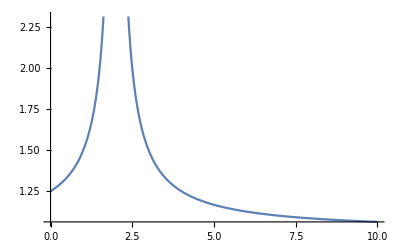

```mathematica
conformalFactor[r_,t_,p_] := 1 + M/(2 shiftedR[r,t,p]);
conformalFactorGradient[r_,t_,p_]:=- M/(2 shiftedR[r,t,p]^2) shiftedRGradient[r,t,p];
Plot[conformalFactor[r, 0, 0], {r, 0, 10}]
```

## Surface integral

```mathematica
surfaceIntegrand[r_, t_, p_]:= 3/(8 Pi M) conformalFactor[r,t,p]^4 normal[r,t,p];
surfaceIntegral[R_] := Integrate[surfaceIntegrand[R, t, p] R^2 Sin[t], {t, 0, Pi}, {p, 0, 2 Pi}] // Flatten
```

```mathematica
surfaceIntegral[3][[3]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.4201×10^-15 and 3.97652×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.42128×10^-16 and 1.94288×10^-12 for the integral and error estimates.

3.58189

```mathematica
Series[surfaceIntegrand[r, 0, 0][[3]] 8 Pi / 3 r^2, {r, Infinity, 10}]
```

{r^2+2 r+11/2+29/(2 r)+593/(16 r^2)+185/(2 r^3)+453/(2 r^4)+546/r^5+1299/r^6+3056/r^7+7120/r^8+16448/r^9+37712/r^10+O[1/r]^11}

```mathematica
For[i=1,i<10,i++,R=10^i;
	Print[R, " => ", surfaceIntegral[R][[3]]// N];
]
```

10 => 2.32082

100 => 2.03016

1000 => 2.003

10000 => 2.0003

100000 => 2.00003

1000000 => 1.99976

10000000 => 2.

100000000 => 8.

1000000000 => 0.

## Volume integral

```mathematica
contractedConformalFactorGradient[r_,t_,p_]:=
	  conformalFactorGradient[r,t,p][[1]] normal[r,t,p][[1]] +
	conformalFactorGradient[r,t,p][[2]] normal[r,t,p][[2]] +
	conformalFactorGradient[r,t,p][[3]] normal[r,t,p][[3]];
volumeIntegrand[{r_, t_, p_}] := 3/(8 Pi M)4 conformalFactor[r,t,p]^3 contractedConformalFactorGradient[r,t,p][[1]] normal[r,t,p] // Simplify // Flatten;
```

```mathematica
volumeIntegrand[{r,t,p}]
volumeIntegrand[ToSphericalCoordinates[{x,y,z}]]
```

{-(3 Cos[p] (r-2 Cos[t]) (1+2 √(4+r^2-4 r Cos[t]))^3 Sin[t])/(32 π (4+r^2-4 r Cos[t])^3),-(3 (r-2 Cos[t]) (1+2 √(4+r^2-4 r Cos[t]))^3 Sin[p] Sin[t])/(32 π (4+r^2-4 r Cos[t])^3),(3 Cos[t] (-r+2 Cos[t]) (1+2 √(4+r^2-4 r Cos[t]))^3)/(32 π (4+r^2-4 r Cos[t])^3)}

{-(3 x (1+2 √(x^2+y^2+(-2+z)^2))^3 (x^2+y^2+(-2+z) z))/(32 π (x^2+y^2+(-2+z)^2)^3 (x^2+y^2+z^2)),-(3 y (1+2 √(x^2+y^2+(-2+z)^2))^3 (x^2+y^2+(-2+z) z))/(32 π (x^2+y^2+(-2+z)^2)^3 (x^2+y^2+z^2)),-(3 (1+2 √(x^2+y^2+(-2+z)^2))^3 z (x^2+y^2+(-2+z) z))/(32 π (x^2+y^2+(-2+z)^2)^3 (x^2+y^2+z^2))}

```mathematica
Series[(1 + 1/r)^4 r^2, {r, Infinity, 10}]
```

r^2+4 r+6+4/r+(1/r)^2+O[1/r]^11

-3/(4 π r^2)-33/(8 π r^3)-261/(16 π r^4)-1779/(32 π r^5)-2775/(16 π r^6)-4077/(8 π r^7)-5733/(4 π r^8)-3897/(π r^9)-10314/(π r^10)+O[1/r]^11

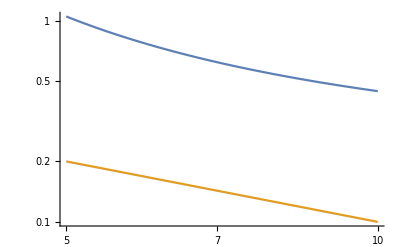

```mathematica
Series[volumeIntegrand[{r, 0, 0}][[3]], {r, Infinity, 10}]
LogLogPlot[{-volumeIntegrand[{r, 0, 0}][[3]] r^2, 1/r}, {r, 5, 10}]
```

```mathematica
volumeIntegrand[{3, 0, p}] // N
```

{0.,0.,-0.805722}

```mathematica
volumeIntegral[Rin_, Rout_] := NIntegrate[volumeIntegrand[{r, t, p}] r^2 Sin[t] ,{r, Rin, Rout}, {t, 0, Pi}, {p, 0, 2 Pi}];
```

```mathematica
volumeIntegral[3, 4]
volumeIntegral[3, 1000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.85654×10^-14 and 1.00319×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.33862×10^-16 and 2.96275×10^-10 for the integral and error estimates.

{9.85654×10^-14,-2.33862×10^-16,-2.47168}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000048235 and 0.00214468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.10669×10^-11 and 6.69337×10^-6 for the integral and error estimates.

{0.000048235,-2.10669×10^-11,-27.187}

```mathematica
For[i=1,i<=10,i++,R=10^i;
	volIntX = volumeIntegral[3, R][[1]] // N;
	volIntZ = volumeIntegral[3, R][[3]] // N;
	volInt = volIntZ - volIntX;
	Print[R, ", ", volIntX, ", ", volIntZ, ", ", volInt];
]
```

## Total integral tests

```mathematica
For[i=1,i<=4,i++,R=10^i;
	surfInt = surfaceIntegral[R][[3]] // N;
	volInt = volumeIntegral[R, 10^5][[3]] // N;
	totalInt = surfInt + volInt;
	Print[R, ", ", surfInt, ", ", volInt, ", ", totalInt];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.71125×10^-12 and 7.17988×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.53477×10^-12 and 4.53126×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.07008×10^-11 and 4.48281×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

10, 0., -1.07008×10^-11, -1.07008×10^-11

100, 0., -2.63256×10^-12, -2.63256×10^-12

1000, 0., -1.32587×10^-11, -1.32587×10^-11

10000, 0., 7.39675×10^-12, 7.39675×10^-12

```mathematica
For[i=1,i<=10,i++,R=10^i;
	surfInt = surfaceIntegral[3][[3]] // N // Flatten;
	volInt = volumeIntegral[3, R][[3]] // N;
	totalInt = surfInt + volInt;
	Print[R, ", ", surfInt, ", ", volInt, ", ", totalInt];
]
```

10, {3.58189}, -7.83573, {-4.25384}

100, {3.58189}, -17.8953, {-14.3134}

1000, {3.58189}, -27.187, {-23.6051}

10000, {3.58189}, -36.4054, {-32.8235}

100000, {3.58189}, -45.6166, {-42.0347}

1000000, {3.58189}, -54.827, {-51.2451}

10000000, {3.58189}, -64.0373, {-60.4554}

100000000, {3.58189}, -73.2476, {-69.6657}

1000000000, {3.58189}, -82.457, {-78.8751}

10000000000, {3.58189}, -91.457, {-87.8751}